```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
𝒞[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1)}]
𝒫[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2}]
ℛ[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->ω1/ω2,ω2->1/ω2}]
𝒮[expr_][ω1_,ω2_]:=ReplaceAll[expr,{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1}]
```

```mathematica
EXPR[ω1_,ω2_][Ma_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=Through[Through[(ℳ0+𝒫[ℳ0[ω1,ω2]]+𝒞[ℳ0[ω1,ω2]]+ℛ[ℳ0[ω1,ω2]]+𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒞[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[ℳ0[ω1,ω2]][ω1,ω2]]+ℛ[𝒫[𝒞[ℳ0[ω1,ω2]][ω1,ω2]][ω1,ω2]]+ℳ1[Ma]+ℛ[ℳ1[Ma][ω1,ω2]])[ω1,ω2]][ϕ1,ϕ2,ϕ3,ϕ4]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=If[ω2>ω1,4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}],0]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
ℳ1[Ma_][ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=((#+𝒮[#][ω1,ω2])&[If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]])+((#+𝒞[#][ω1,ω2])&[If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]])(*+((#+𝒮[#][ω1,ω2]+𝒫[#][ω1,ω2]+𝒞[#][ω1,ω2])&[If[(ω2>ω1)&&(ω1>1),-(4 π)/NcNIntegrate[(2rcp rcn+2rdp rcn+Ma^2/(x-ω1)+Ma^2/(x-1)-Ma^2/(x-ω1+ω2)-Ma^2/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}],0]])*)
```

```mathematica
ℳone[ω1_,ω2_][Ma_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR[ω1,ω2][Ma][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;g=1;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ωfp[z_][M1_,M2_,M3_,M4_]:=(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 1.*)
```

```mathematica
ωfn[z_][M1_,M2_,M3_,M4_]:=(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))(*transform z to ω (Barbon), solution 2*)
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
ω2n[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1);(*transform ω1 to ω2, your definition, solution 2*)
```

```mathematica
Sz[z_][M1_,M2_]:=M1^2/(1-z)+M2^2/z;(*Centre of mass energy*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
zfω1[ω1_][MA_,MB_,MC_,MD_]:=ω1/(1+ω2n[ω1][MA,MB,MC,MD])(*transform ω1 to z, using z=ω1/(1+ω2) and previous result of ω1 to ω2*)
ωfω1[ω1_][MA_,MB_,MC_,MD_]:=(ω2n[ω1][MA,MB,MC,MD])/(1+ω2n[ω1][MA,MB,MC,MD]);
```

```mathematica
ω1fz[z_][M1_,M2_,M3_,M4_]:=-z/(ωfp[z][M1,M2,M3,M4]-1);
ω2fz[z_][M1_,M2_,M3_,M4_]:=(-ωfp[z][M1,M2,M3,M4])/(ωfp[z][M1,M2,M3,M4]-1);(*transform z to ω1 and ω2, using z=ω1/(1+ω2) and previous result of z to ω*)
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,
(*Print["ω1=",ω1,"    ω2=",ω2];*)(*it's for debug purpose, you can comment this*){Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]],{ω1,0.003,0.5,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

```mathematica
Msumdat=Msum[60][0,0,0,0]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 18.2875 and 2.67683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.500003}. NIntegrate obtained 0.566422 and 0.08291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 12.9545 and 1.89622 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 9.14359 and 1.3384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.500003}. NIntegrate obtained 0.337839 and 0.0494512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 1.39234 and 0.203804 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.844124,0.500003}. NIntegrate obtained 2.09038 and 0.305979 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 6.41779 and 0.939405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 18.2875 and 2.67683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.719179 and 0.10527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 15.397 and 2.25374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 10.8897 and 1.59398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 2.54205 and 0.372092 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 7.6668 and 1.12223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 21.71 and 3.17781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.719179 and 0.10527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 15.397 and 2.25374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 3.07859 and 0.450629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.0370768 and 0.00542711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.903807 and 0.132295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.092514 and 0.0135417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 4.46899 and 0.654149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 51.1477 and 7.48678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 36.2856 and 5.31132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 21.71 and 3.17781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 60.7711 and 8.89541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.000134966 and 0.0000197556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.0091578 and 0.00134047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.187341 and 0.027422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.0370768 and 0.00542711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 3.07859 and 0.450629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.903807 and 0.132295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.0925139 and 0.0135417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 4.46899 and 0.654149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 85.9848 and 12.5861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 43.072 and 6.30469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.440671 and 0.0645032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 1.71073 and 0.250409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 102.425 and 14.9926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 3.715 and 0.543783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.000134966 and 0.0000197556 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.0091578 and 0.00134047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.187341 and 0.027422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 85.9848 and 12.5861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 174.436 and 25.5332 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 25.7656 and 3.77145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 145.864 and 21.351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.440671 and 0.0645032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 72.2559 and 10.5765 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 1.71073 and 0.250409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 208.941 and 30.584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.254398 and 0.0372375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 301.422 and 44.1209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 72.2559 and 10.5765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 25.7656 and 3.77145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 363.143 and 53.1555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 1.12598 and 0.164815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.0607039 and 0.00888552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 5.36164 and 0.784811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.134107 and 0.01963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 122.15 and 17.8798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.254398 and 0.0372375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 301.422 and 44.1209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 1.12598 and 0.164815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 30.5755 and 4.4755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.0607039 and 0.00888552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 5.36164 and 0.784811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.134107 and 0.01963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 122.15 and 17.8798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.00272269 and 0.000398532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 0.0202815 and 0.0029687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 250.715 and 36.6987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 530.775 and 77.6928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.500003,0.844124}. NIntegrate obtained 438.495 and 64.1852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.00272269 and 0.000398532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 0.0202815 and 0.0029687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 250.715 and 36.6987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 530.775 and 77.6928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.499999,0.844124}. NIntegrate obtained 438.495 and 64.1852 for the integral and error estimates.

{{120.335,120.335,120.335,120.335},{{2203.6,-0.00215945+(2 ℳ0[0.003,0.003])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[333.333,333.333])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.003,0.003]])[0.003,0.003][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{1069.13,-0.043563+(2 ℳ0[0.013,0.013])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[76.9231,76.9231])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.013,0.013]])[0.013,0.013][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{811.717,-0.146525+(2 ℳ0[0.023,0.023])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[43.4783,43.4783])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.023,0.023]])[0.023,0.023][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{684.284,-0.324504+(2 ℳ0[30.303,30.303])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(3 ℳ0[30.303,0.033])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{605.262,-0.593229+(2 ℛ[ℳ0[23.2558,23.2558]])[0.043,0.043][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{550.406,-0.971263+(2 ℳ0[0.053,0.053])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[18.8679,18.8679])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.053,0.053]])[0.053,0.053][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{509.631,-1.48022+(2 ℳ0[15.873,15.873])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[15.873,15.873])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{477.894,-2.14572+(2 ℳ0[13.6986,13.6986])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[13.6986,13.6986]])[0.073,0.073][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{452.358,-2.99745+(2 ℳ0[12.0482,12.0482])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[12.0482,12.0482]])[0.083,0.083][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{431.292,-4.07037+(2 ℳ0[0.093,0.093])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.093,0.093]])[0.093,0.093][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.093,0.093]])[0.093,0.093][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[10.7527,10.7527]])[0.093,0.093][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{413.571,-2.70271+(2 ℳ0[0.103,0.103])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.103,0.103]])[0.103,0.103][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.103,0.103]])[0.103,0.103][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[9.70874,9.70874]])[0.103,0.103][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{398.427,-7.05074+(2 ℳ0[8.84956,8.84956])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[8.84956,8.84956]])[0.113,0.113][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{385.319,-4.53137+(2 ℳ0[0.123,0.123])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.123,0.123]])[0.123,0.123][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.123,0.123]])[0.123,0.123][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[8.13008,8.13008]])[0.123,0.123][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{373.85,-11.5069+(2 ℳ0[0.133,0.133])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.133,0.133]])[0.133,0.133][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.133,0.133]])[0.133,0.133][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[7.5188,7.5188]])[0.133,0.133][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{363.723,-14.4609+(2 ℳ0[6.99301,6.99301])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[6.99301,6.99301]])[0.143,0.143][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{354.713,-18.0157+(2 ℳ0[6.53595,6.53595])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[6.53595,6.53595]])[0.153,0.153][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{346.64,-11.1387+(2 ℳ0[0.163,0.163])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.163,0.163]])[0.163,0.163][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.163,0.163]])[0.163,0.163][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[6.13497,6.13497]])[0.163,0.163][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{339.366,-27.3718+(2 ℳ0[5.78035,5.78035])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[5.78035,5.78035]])[0.173,0.173][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{332.776,-16.723+(2 ℳ0[0.183,0.183])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.183,0.183]])[0.183,0.183][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.183,0.183]])[0.183,0.183][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[5.46448,5.46448]])[0.183,0.183][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{326.779,-20.3364+(2 ℳ0[0.193,0.193])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.193,0.193]])[0.193,0.193][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.193,0.193]])[0.193,0.193][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[5.18135,5.18135]])[0.193,0.193][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{321.3,-49.2574+(2 ℳ0[4.92611,0.203])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[4.92611,4.92611])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{316.274,-29.72+(2 ℳ0[0.213,0.213])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.213,0.213]])[0.213,0.213][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.213,0.213]])[0.213,0.213][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[4.69484,4.69484]])[0.213,0.213][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{311.65,-71.5038+(2 ℳ0[4.4843,0.223])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[4.4843,4.4843])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{307.382,-85.7862+(2 ℳ0[4.29185,4.29185])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[4.29185,4.29185]])[0.233,0.233][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{303.432,-51.3423+(2 ℳ0[0.243,0.243])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[4.11523,4.11523])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.243,0.243]])[0.243,0.243][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{299.767,-61.3344+(2 ℳ0[0.253,0.253])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.253,0.253]])[0.253,0.253][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.253,0.253]])[0.253,0.253][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.95257,3.95257]])[0.253,0.253][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{296.359,-73.1487+(2 ℳ0[0.263,0.263])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.263,0.263]])[0.263,0.263][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.263,0.263]])[0.263,0.263][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.80228,3.80228]])[0.263,0.263][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{293.184,-87.1175+(2 ℳ0[0.273,0.273])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.273,0.273]])[0.273,0.273][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.273,0.273]])[0.273,0.273][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.663,3.663]])[0.273,0.273][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{290.219,-103.636+(2 ℳ0[0.283,0.283])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.283,0.283]])[0.283,0.283][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(3 ℛ[ℳ0[0.283,0.283]])[0.283,0.283][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{287.447,-246.352+(2 ℳ0[0.293,0.293])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.293,0.293]])[0.293,0.293][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.293,0.293]])[0.293,0.293][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.41297,3.41297]])[0.293,0.293][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{284.85,-292.599+(2 ℳ0[0.303,0.303])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.303,0.303]])[0.303,0.303][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.303,0.303]])[0.303,0.303][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.30033,3.30033]])[0.303,0.303][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{282.414,-347.36+(2 ℳ0[0.313,0.313])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.313,0.313]])[0.313,0.313][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.313,0.313]])[0.313,0.313][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.19489,3.19489]])[0.313,0.313][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{280.125,-412.25+(2 ℳ0[3.09598,3.09598])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.09598,3.09598]])[0.323,0.323][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{277.972,-244.604+(2 ℳ0[0.333,0.333])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.333,0.333]])[0.333,0.333][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.333,0.333]])[0.333,0.333][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[3.003,3.003]])[0.333,0.333][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{275.945,-290.284+(2 ℳ0[0.343,0.343])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.343,0.343]])[0.343,0.343][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.343,0.343]])[0.343,0.343][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.91545,2.91545]])[0.343,0.343][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{274.033,-344.576+(2 ℳ0[0.353,0.353])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.353,0.353]])[0.353,0.353][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.353,0.353]])[0.353,0.353][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.83286,2.83286]])[0.353,0.353][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{272.23,-409.182+(2 ℳ0[0.363,0.363])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.363,0.363]])[0.363,0.363][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.363,0.363]])[0.363,0.363][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.75482,2.75482]])[0.363,0.363][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{270.526,-486.169+(2 ℳ0[0.373,0.373])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.373,0.373]])[0.373,0.373][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.373,0.373]])[0.373,0.373][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.68097,2.68097]])[0.373,0.373][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{268.915,-1156.09+(2 ℳ0[0.383,0.383])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[2.61097,2.61097])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.383,0.383]])[0.383,0.383][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{267.392,-1375.76+(2 ℳ0[0.393,0.393])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.393,0.393]])[0.393,0.393][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.393,0.393]])[0.393,0.393][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.54453,2.54453]])[0.393,0.393][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{265.949,-819.401+(2 ℳ0[0.403,0.403])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.403,0.403]])[0.403,0.403][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.403,0.403]])[0.403,0.403][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.48139,2.48139]])[0.403,0.403][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{264.582,-1954.4+(2 ℳ0[2.42131,0.413])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[2.42131,2.42131])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{263.286,-1166.91+(2 ℳ0[0.423,0.423])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.423,0.423]])[0.423,0.423][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.423,0.423]])[0.423,0.423][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.36407,2.36407]])[0.423,0.423][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{262.057,-1395.49+(2 ℳ0[0.433,0.433])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.433,0.433]])[0.433,0.433][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.433,0.433]])[0.433,0.433][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.30947,2.30947]])[0.433,0.433][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{260.89,-1671.53+(2 ℳ0[0.443,0.443])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.443,0.443]])[0.443,0.443][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.443,0.443]])[0.443,0.443][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.25734,2.25734]])[0.443,0.443][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{259.782,-4011.44+(2 ℳ0[2.20751,2.20751])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.20751,2.20751]])[0.453,0.453][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{258.73,-4822.75+(2 ℳ0[0.463,0.463])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.463,0.463]])[0.463,0.463][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.463,0.463]])[0.463,0.463][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.15983,2.15983]])[0.463,0.463][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{257.73,-2905.15+(2 ℳ0[0.473,0.473])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 𝒫[ℳ0[0.473,0.473]])[0.473,0.473][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[0.473,0.473]])[0.473,0.473][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.11416,2.11416]])[0.473,0.473][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{256.78,-7015.91+(2 ℳ0[2.07039,0.483])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℳ0[2.07039,2.07039])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]},{255.876,-8492.4+(2 ℳ0[2.0284,2.0284])[ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]+(2 ℛ[ℳ0[2.0284,2.0284]])[0.493,0.493][ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300],ϕn[0][ΦB$4300]]}}}

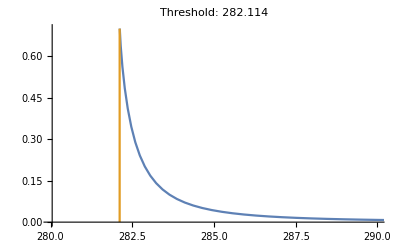

```mathematica
ListPlot[{Select[Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.7}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

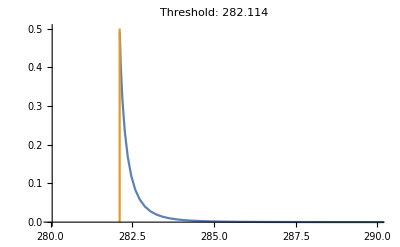

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],0.5}}},PlotRange->{{280,290},All},Joined->True,PlotLabel->"Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[5];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[5];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

-56702.2

```mathematica
λ=10^-3;
```

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

NIntegrate::nlim: y = -1.×10^-6+1.10195 (0.198703+0.708776 x) 不是积分的一个有效的极限.

$Aborted

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

574551.

```mathematica
Table[Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];((#+𝒮[#][ω1,ω2])&[If[1>ω1,-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}]),0]])],{λ,Table[10^-m,{m,0,10}]}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

{-2.06510737652442×10^698,-60.1637-1.36561×10^104 ⅈ,406.722-2.22264×10^14 ⅈ,1632.58,11989.3,115365.,1.1491×10^6,1.14865×10^7,1.14864×10^8,1.1486×10^9,1.1486×10^10}

```mathematica
Solve[(y-1) ω1+(1-x)ω2==0,y]
```

{{y→(ω1-ω2+x ω2)/ω1}}